```mathematica
(*长直导线的电场分布*)
```

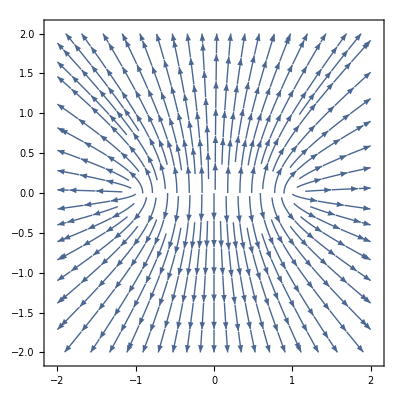

-Graphics3D-

```mathematica
L=1;λ=1;
V[x_,y_]:=λ(Log[L+x+√((-L-x)^2+y^2)]-Log[-L+x+√((-L+x)^2+y^2)]);
Ex[x_,y_]=-D[V[x,y],x];
Ey[x_,y_]=-D[V[x,y],y];
StreamPlot[{Ex[x,y],Ey[x,y]},{x,-2,2},{y,-2,2}]
Plot3D[V[x,y],{x,-2,2},{y,-1,1}]
```

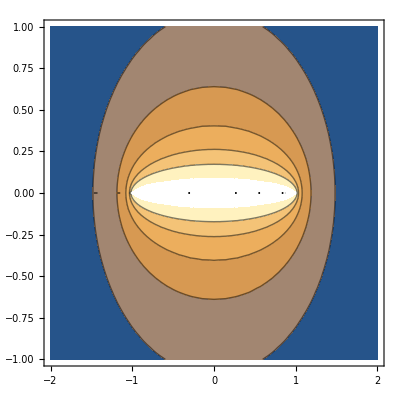

```mathematica
ContourPlot[V[x,y],{x,-2,2},{y,-1,1},Contours->5]
```